## Axon-Hillock Analysis

We found that using a delayed inverter, although it creates nice looking oscillatory waveforms, operates too slow and doesn’t resolve the linearity problem we were seeing with the starved inverters.  The linearity problem we were seeing was that the period of an oscillation didn’t vary linearly with the input current (or throttling current), I_in.  As such, Ben suggested that we look into the Axon-Hillock circuit that he uses in the pulse extender, which comes from Carver’s book.  This notebook will have any of the Mathematica based analysis that we perform on this AH circuit.

Background/Setup

In this sub-chapter, I try to define the situation and how we are performing our analysis.  The reference circuit for my analysis is shown below.

## Capacitor divider background

The first thing we need to understand is how a capacitor divider circuit operates because the fundamental analysis of an axon-hillock circuit requires understanding the mechanism of the capacitor divider in the middle of the circuit, comprised of C_1 and C_2.

### Parallel Caps → Serial Caps

At time t=0, we can assume that the capacitor circuit switches from the first configuration below to the second configuration.  The first configuration is two capacitors in parallel and the second configuration is two capacitors in series (forming a capacitor divider).  What this implies is that when t=0, V_o goes from 0 to 1 (or from Gnd to V_dd).  V_o is named because it the voltage of the output node from this circuit.  The circuit’s output (V_o) forms an oscillatory square wave.

-Graphics-  →^(t=0)

Based on the basic circuit equation Q=C·V and the fact that two caps in parallel is the same as the one cap equal to the sum of the two cap’s capacitances, we know that when t<0, the overall charge across the circuit on the left is defined as follows:
	Q_0=(C_1+C_2)V_i 
where V_i is the initial voltage of V_c @ t=0.

At t=0, we know the circuit changes modes from the circuit on the left to the circuit on the right.  We assume this change happens near instantaneously.  Because of this we also know that Q_0=Q_1-Q_2, where Q_1 and Q_2 are the charges on the two capacitors individually, because the charge doesn’t escape instantaneously.  We also note that the charge for Q_2 is negative.  This is purely because the charges built up at V_c before t=0, are positive and the charges on the other side of the plate’s are negative.  At t=0, these positive charges are on the wrong side of the C_2’s plates and so there is, what appears to be, a negative charge across C_2.

We also know that the following equations are true for Q_1 and Q_2.
	Q_1=C_1·V_c
	Q_2=C_2·(V_dd-V_c)
As such, the following equations becomes the state of the circuit’s charge at t=0, because no charge can magically move/change/disappear in an instant.
	Q_0=Q_1-Q_2
	(C_1+C_2)V_i=C_1·V_c-C_2·(V_dd-V_c)
	(C_1+C_2)V_i=C_1·V_c- C_2·V_dd+C_2·V_c
	(C_1+C_2)V_i+C_2·V_dd=(C_1+C_2)V_c
	V_i+C_2/(C_1+C_2)·V_dd=V_c
	V_c=V_i+C_2/(C_1+C_2)·V_dd

V_c=V_i+ΔV
ΔV=C_2/(C_1+C_2)·V_dd

This essentially says that at t=0, the voltage at V_c will have a nearly instantaneous change equal to ΔV.  ΔV is equal to the capacitor divider ratio multiplied by V_dd.

### Serial Caps → Parallel Caps

Going the other way, if we assumed that at t=0, we started in the serial configuration, and then it switched instantaneously to the parallel configuration, as shown below, then the following math describes the circuit’s behavior.  This is the same as saying when V_o goes from 1 to 0 (or from V_dd to Gnd), the following math applies.

→^(t=0) -Graphics-

This math is essentially the same as the math above, except that anywhere it used to say V_i above, it should now say V_c in this math, and vice-versa.  This is because the initial condition V_i is the voltage at which the V_csits at t=0.  Then we want to see how V_c changes in the parallel circuit.
	Q_0=Q_1-Q_2
	(C_1+C_2)V_c=C_1·V_i-C_2·(V_dd-V_i)
	(C_1+C_2)V_c=C_1·V_i- C_2·V_dd+C_2·V_i
	(C_1+C_2)V_c=(C_1+C_2)V_i-C_2·V_dd
	V_c=V_i-C_2/(C_1+C_2)·V_dd

V_c=V_i-ΔV
ΔV=C_2/(C_1+C_2)·V_dd

### Summary of capacitor behavior

These two conclusions mean that the following equation is true, anytime the circuit switches between these two modes, depending on which way the circuit switches:

V_c=V_i±ΔV
ΔV=C_2/(C_1+C_2)·V_dd

## Circuit Derivation

### Background and general equations

Now that we have an understanding of how the capacitor divider operates and a mathematical model of its behavior, we can analyze the AH circuit above.  The first thing to note is that the circuit has three inverters, denoted I_1, I_2, and I_3.  These inverters are drawn above using transistors PI_x and NI_x, where x is the number of the inverter.  There are also two transistors that serve as the “current sources”, P_1 and N_1.  These current sources determine how quickly the joint capacitors C_1 and C_2 charge or discharge.  In other words, the circuit can be described as having three main components: inverters, a capacitor divider (which changes behavior based on V_o’s voltage), and current sources.

When V_o switches, as a result of V_c crossing the inversion point of I_1, the capacitor divider will change between the two modes of the capacitor divider circuit analyzed in the previous section.  Also, when V_o switches, I_3, disables either PI_3 or NI_3, which changes the mode of the circuit from charging the caps to discharging the caps.  As such, the duration of this switching occurrence is determined by how quickly the caps charge/discharge.

For the purposes of the math below, we assume that V_c sits at some average value V_i, from which the ΔV switch occurs.  For durations t_lo and t_hi, the circuit will either charge or discharge depending whether or not V_o is low or high, respectively.  Said another way, when V_o is low, the circuit is charging, and when V_o is high, the circuit is discharging.

First we know from basic circuit’s equations that the following equation are true, where we need to define I, C, and dV/dt.
	I=C dV/dt
The voltage that we are changing over time is V_c, and therefore we are actually measuring the rate of change as follows:
	dV/dt=dV_c/dt
In this circuit, the rate of current that charges/discharges the capacitors can always be defined as follows (Note: The direction of current flow (whether it’s in to or out of the node V_c merely determines the fact that I is charging or discharging.  As such, I’ve made the generality that the only thing that matters is the sum of the two independent currents):
	I=I_P1+I_N1
Also, regardless of the mode that the circuit is in, we know that the change in the voltage (ΔV) is equal to the instantaneous jump that the capacitor divider moved.
	ΔV=C_2/(C_1+C_2)·V_dd
There is one main difference between the charging mode and discharging mode.  The difference is that I_P1 and I_N1 behave differently in the two modes.  The mathematical derivation for these two modes is defined below to calculate what t_lo and t_hi equal in each mode.

### Charging the capacitors

In the charging mode, we can assume a couple of the following things.  The first thing we assume is that V_o is set to GND or 0V.  This also implies that the capacitors are in a parallel configuration.  The second thing that follows from the first assumption is that V_s is equal to 1, because it is the inverted output of V_o.  The second assumption that we can make is that V_o and V_s transition instantaneously.  As such, when the circuit is charging the capacitors, the equivalent capacitance is equal to the sum of the two capacitors.
	C=C_1+C_2
We also know that when V_s=1, transistor P_1 forms a perfect current mirror with its bias and as such:
	I_P1=I_in		 (Note: we are assuming no mismatch in the transistors).
I_N1 on the other hand is not a simple current mirror because its source node is now V_c.  As such the following math applies for the current flowing through N_1. (Note: we are assuming κ to equal 1 for this math).
	I_in=I_0 e^(V_n/U_t)
	I_N1=I_0 e^((V_n-V_c)/U_t)
	I_N1=I_in e^(-V_c/U_t)
At t=0, as shown in the capacitor divider analysis above, there is an instantantaneous change in V_c’s value.  This change happens when V_c is equal to the inversion voltage of inverter I_1.  Immediately after this point, the inverter flips and the circuit changes behavior.  As such, V_i - ΔV becomes the starting point from which V_c begins to charge back to V_i.  The amount of time it takes to charge back to V_i will determine the period that the circuit’s output, V_o, will stay low.  We call this period t_lo.   (Note:  Another assumption that we make is that this inversion point is the same regardless of whether V_c is charging or discharging).  Now that we have fully defined I and C, we can see put them into the dynamical system equation from above to get a working equation for how V_c changes:
	C dV_c/dt=I
	(C_1+C_2)dV_c/dt=I_P1+I_N1
	(C_1+C_2)dV_c/dt=I_in+I_in e^(-V_c/U_t)

(C_1+C_2)/I_in dV_c/dt=1+e^(-V_c/U_t)

### Solve charging dynamical equation

```mathematica
FullSimplify[DSolve[{(C1+C2)/Iin Vc'[t]==1+ⅇ^((-Vc[t])/Ut),Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[-1+ⅇ^((Iin t)/((C1+C2) Ut)) (1+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut))]}}

```mathematica
VcCharge[t_,Ut_]:=Ut Log[-1+ⅇ^((Iin t)/((C1+C2) Ut))(1+ⅇ^((-C2/(C1+C2)Vdd+Vinv)/Ut))]
```

### Discharging the capacitors

When the circuit is discharging the capacitors, the math is similar.  The equivalent capacitance is the same as before, because in DC analysis, the V_dd point and V_gnd are both static, so the capacitors act as if they are both shorted to the same point.
	C=C_1+C_2
Similar to the math in the charging section, we can derive the currents I_N1 and I_P1.  It should be noted here that the overall direction of I is now going to be negative, because the current is discharging the capacitors.  In other words, because the current is leaving node V_c, we denote the current I to be negative.  First, we know that when V_s=0, unlike the charging circuit, transistor N_1 forms a perfect current mirror with its bias and as such:
	I_N1=I_in		 (Note: we are assuming no mismatch in the transistors).
Analogously to the charging circuit, I_P1 is now the current that is not a simple current mirror.  Its source node is now V_c.  As such the following math applies for the current flowing through N_1. (Note: we are assuming κ to equal 1 for this math).
	I_in=I_0 e^((V_dd-V_p)/U_t)
	I_P1=I_0 e^((V_c-V_p)/U_t)
	I_P1=I_0 e^((V_c-V_dd+V_dd-V_p)/U_t)
	I_P1=I_0 e^((V_dd-V_p)/U_t)e^((V_c-V_dd)/U_t)
	I_P1=I_in e^((-(V_dd-V_c))/U_t)
Now that we have redefined C and I for the discharging circuit, we perform the same math that we did before:
	C dV_c/dt=I
	(C_1+C_2)dV_c/dt=-(I_P1+I_N1)
	(C_1+C_2)dV_c/dt=-(I_in e^((-(V_dd-V_c))/U_t)+I_in)

(C_1+C_2)/I_in dV_c/dt=-(1+e^((-(V_dd-V_c))/U_t))

### Solve discharging dynamical equation

```mathematica
FullSimplify[DSolve[{(C1+ C2)/Iin Vc'[t]==-(1+ⅇ^((-(Vdd-Vc[t]))/Ut)),Vc[0]==Vinv+C2/(C1+C2)Vdd},Vc[t],t]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Vdd-Ut Log[-1+ⅇ^((Iin t)/((C1+C2) Ut))+ⅇ^((Iin t+C1 Vdd-(C1+C2) Vinv)/((C1+C2) Ut))]}}

```mathematica
VcDischarge[t_,Ut_]:=Vdd-Ut Log[-1+ⅇ^((Iin t)/((C1+C2) Ut)) +ⅇ^((Iin t + C1 Vdd-(C1+C2)Vinv)/((C1+C2) Ut))]
```

### Difference between charging an discharging solutions

```mathematica
FullSimplify[DSolve[{Ceq/Iin Vc'[t]==1+ⅇ^((-Vc[t])/Ut),Vc[0]==Vinv-C2/(C1+C2)Vdd},Vc[t],t]]
FullSimplify[DSolve[{Ceq/Iin Vc'[t]==-(1+ⅇ^((-(Vdd-Vc[t]))/Ut)),Vc[0]==Vinv+C2/(C1+C2) Vdd},Vc[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Ut Log[-1+ⅇ^((Iin t)/(Ceq Ut)) (1+ⅇ^((-(C2 Vdd)/(C1+C2)+Vinv)/Ut))]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Vc[t]→Vdd-Ut Log[-1+ⅇ^((Iin t)/(Ceq Ut)) (1+ⅇ^((C1 Vdd)/(C1 Ut+C2 Ut)-Vinv/Ut))]}}

### Plot of V_c waveform

```mathematica
Vc[t_]:=Piecewise[{{VcCharge, t<(Vdd-Vinv)/mi}, {VcDischarge, (Vdd-Vinv)/mi≤t≤-Vinv/mi}}]
```

```mathematica
UtFunc[T_]:=QuantityMagnitude[UnitSimplify[UnitConvert[Quantity[T ,"DegreesCelsius"],"Kelvins"]*Quantity["BoltzmannConstant"] /Quantity["ElementaryCharge"]]];
```

```mathematica
UtFunc[#]&/@{0,25,50}
```

{0.023538,0.025693,0.027847}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

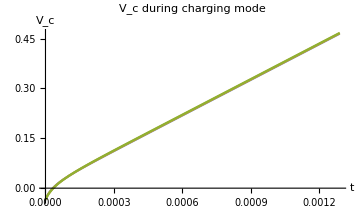
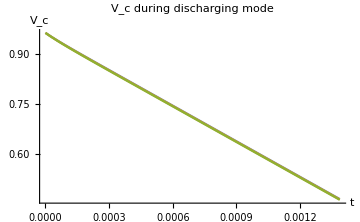
Charging period (t_lo) | Discharging period (t_hi)
{0.00128857,0.0012856,0.00128248} | {0.00138657,0.0013836,0.00138048}
Error over temp: 0.473871% | Error over temp: 0.440306%
Full period (t_lo+t_hi) | 
{0.00267514,0.0026692,0.00266295} | Avg period: 0.00266909
Error over temp: 0.456472% | 
-Graphics- | -Graphics-

```mathematica
Block[{Vdd=1, Vinv=0.465, Ut1=UtFunc[0],Ut2=UtFunc[25],Ut3=UtFunc[50], C1=.14*10^-15,C2=140*10^-18, Iin=100*10^-15,tMax11, tMax12, tMax13, tMax21,tMax22,tMax23,ts},
tMax11=t/.Solve[VcCharge[t,Ut1]==Vinv, t]⟦1⟧;
tMax12=t/.Solve[VcCharge[t,Ut2]==Vinv, t]⟦1⟧;
tMax13=t/.Solve[VcCharge[t,Ut3]==Vinv, t]⟦1⟧;
tMax21=t/.Solve[VcDischarge[t,Ut1]==Vinv, t]⟦1⟧;
tMax22=t/.Solve[VcDischarge[t,Ut2]==Vinv, t]⟦1⟧;
tMax23=t/.Solve[VcDischarge[t,Ut3]==Vinv, t]⟦1⟧;
ts={tMax11, tMax12, tMax13}+{tMax21, tMax22, tMax23};
Grid[{
(*{{ Ut1,Ut2, Ut3},{ Vinv, Vdd}},*)
{Row[{"Charging period (t_lo)"}],Row[{"Discharging period (t_hi)"}]},
{{tMax11, tMax12, tMax13},{tMax21, tMax22, tMax23}},
{Row[{"Error over temp: ",(tMax11-tMax13)*100/Mean[{tMax11,tMax12,tMax13}], "%"}],Row[{"Error over temp: ",(tMax21-tMax23)*100/Mean[{tMax21,tMax22,tMax23}], "%"}]},
{Row[{"Full period (t_lo+t_hi)"}]},
{ts,Row[{"Avg period: ", Mean[ts]}]},
{Row[{"Error over temp: ", (ts⟦1⟧-ts⟦3⟧)*100/Mean[ts], "%"}]},
{
Show[
Plot[{VcCharge[t,Ut1],VcCharge[t,Ut2],VcCharge[t,Ut3]},{t,0,tMax11}, 
ImageSize->Medium,PlotLabel->"V_c during charging mode",AxesLabel->{"t", "V_c"}]
],
Show[
Plot[{VcDischarge[t,Ut1],VcDischarge[t,Ut2],VcDischarge[t,Ut3]},{t,0,tMax21},
ImageSize->Medium,PlotLabel->"V_c during discharging mode",AxesLabel->{"t", "V_c"}]
]}
}]
]
```

## Appendix